Question 1
1.	Over the region  -15 cm < x < 15 cm and -15 cm < y < 15 cm, construct the following representations of the electric potential for the charge arrangement shown in the plot below:
a)	3-d equipotential surface (use ListCountourPlot3D)
b)	2-d contour map (use ListCountourPlot)
c)	3-d elevation graph (use ListPlot3D)
Question 2
2	a) Using the same arrangement as in Problem 1, make a plot of the electrical potential energy for a proton along the x-axis from -15 cm to +15 cm.
      b) If the proton starts from rest at the origin, what will be its speed at x = 15.0  
           cm?

```mathematica
q1=-2.7*10^-9;
q2=10.4*10^-9;
q3=-8.3*10^-9;
q4=6.5*10^-9;
coulombConstant=8.99*10^9;
x1=-0.06;
y1=0.06;
x2=0.06;
y2=0.06;
x3=0.06;
y3=-0.06;
x4=-0.06;
y4=-0.06;
Vsave=Table[0,{31},{31},{31}];
V2save=Table[0,{31},{31}];
Usave=Table[0,{31}];
Xsave=Table[0,{31}];
r[x_,y_,z_,xp_,yp_,zp_]:=Sqrt[(x-xp)^2+(y-yp)^2+(z-zp)^2];
V[q_,r_]:=coulombConstant*q/r;
For[k=1,k<32,k=k+1,
For[i=1,i<32,i=i+1,
For[j=1,j<32,j=j+1,
x=-0.15+(i-1)*0.01;
y=-0.15+(j-1)*0.01;
z=-0.15+(k-1)*0.01;
dist1=r[x,y,z,x1,y1,0];
dist2=r[x,y,z,x2,y2,0];
dist3=r[x,y,z,x3,y3,0];
dist4=r[x,y,z,x4,y4,0];
Vsave[[i,j,k]]=V[q1,dist1]+V[q2,dist2]+V[q3,dist3]+V[q4,dist4];
If[dist1==0,Vsave[[i,j,k]]=(Vsave[[i,j-1,k]]+Vsave[[i-1,j,k]]+Vsave[[i,j,k-1]])/3];
If[dist2==0,Vsave[[i,j,k]]=(Vsave[[i,j-1,k]]+Vsave[[i-1,j,k]]+Vsave[[i,j,k-1]])/3];
If[dist3==0,Vsave[[i,j,k]]=(Vsave[[i,j-1,k]]+Vsave[[i-1,j,k]]+Vsave[[i,j,k-1]])/3];
If[dist4==0,Vsave[[i,j,k]]=(Vsave[[i,j-1,k]]+Vsave[[i-1,j,k]]+Vsave[[i,j,k-1]])/3];
If[k==16,V2save[[i,j]]=Vsave[[i,j,k]]];
If[k==16,
If[j==16,{Usave[[i]]=1.6*10^-19*Vsave[[i,j,k]],Xsave[[i]]=x}]]
]
]
]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

-Graphics3D-

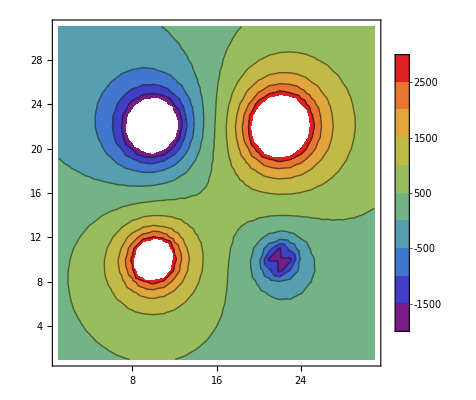

-Graphics3D-

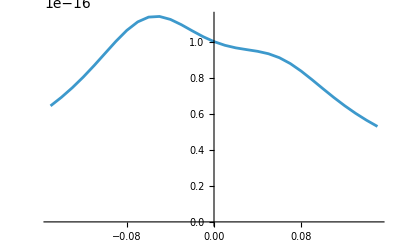

```mathematica
ListContourPlot3D[Vsave,Contours->15,Mesh->None,ContourStyle->Opacity[0.45]]
ListContourPlot[V2save,ContourShading->Automatic,ColorFunction->"Rainbow",PlotLegends->Automatic]
ListPlot3D[V2save,PlotTheme->"Web",ColorFunction->"Rainbow",PlotLegends->Automatic]
data=Thread[{Xsave,Usave}];
ListLinePlot[data]

(*RegionFunction->Function[{x,y,z},13<x]*)
```

```mathematica
mp=1.67*10^-27;
velec=Sqrt[2*(Usave[[16]]-Usave[[31]])/mp];
Print[velec]
```

237407.

Question 3
	Create a contour map and a streamplot of a ±5C dipole separate by 10 cm, centered on a region  -10 cm < x < 10 cm and -10 cm < y < 10 cm, that looks similar to the figure 7.31.

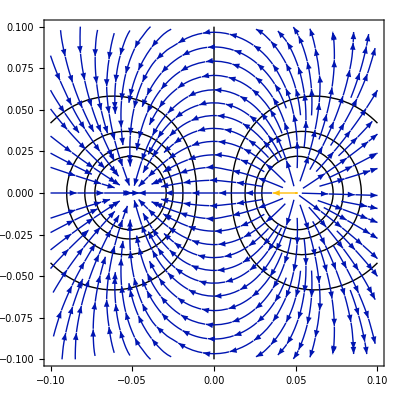

```mathematica
Q1=-5;
Q2=5;
X1=-0.05;
X2=0.05;
Y1=0;
Y2=0;
r[x_,xp_,y_,yp_] :=Sqrt[(x-xp)^2+(y-yp)^2]
Ex[q_,x_,xp_,y_,yp_]:=coulombConstant*q*(x-xp)/r[x,xp,y,yp]^3;
Ey[q_,x_,xp_,y_,yp_]:=coulombConstant*q*(y-yp)/r[x,xp,y,yp]^3;
Extot[x_,y_]:=Ex[Q1,x,X1,y,Y1]+Ex[Q2,x,X2,y,Y2];
Eytot[x_,y_]:=Ey[Q1,x,X1,y,Y1]+Ey[Q2,x,X2,y,Y2];
V[q_,x_,xp_,y_,yp_]:=coulombConstant*q/r[x,xp,y,yp];
Vtot[x_,y_]:=V[Q1,x,X1,y,Y1]+V[Q2,x,X2,y,Y2];
as=VectorPlot[{Extot[x,y],Eytot[x,y]},{x,-.10,.10},{y,-.10,.10},VectorColorFunction->"Rainbow"];
bs=StreamPlot[{Extot[x,y],Eytot[x,y]},{x,-.10,.10},{y,-.10,.10}];
cs=ContourPlot[Vtot[x,y],{x,-.10,.10},{y,-.10,.10},Contours->9,ContourShading->None];
Show[cs,bs]
```